```mathematica
$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;
repl={kx->k Sin[θ] Cos[ϕ],ky->k Sin[θ] Sin[ϕ],kz->k Cos[θ]};
ass=Assumptions->{kx,ky,kz,k,θ,χ,ϕ,θp,ϕp,kp,vinter,vinter} ∈ Reals && k>0 && kp>0 && 0<=θ<=π && 0<=θp<=π && vintra>0 && vinter>0;
```

## Computing W_kk'

```mathematica
sx=({{0, 1/(√2), 0}, {1/(√2), 0, 1/(√2)}, {0, 1/(√2), 0}});sy=1/(√2)({{0, -ⅈ, 0}, {ⅈ, 0, -ⅈ}, {0, ⅈ, 0}});sz=({{1, 0, 0}, {0, 0, 0}, {0, 0, -1}});
(*********)
Clear[ham];
repl={kx->k Sin[θ] Cos[ϕ],ky->k Sin[θ] Sin[ϕ],kz->k Cos[θ]};
ham[χ_]= χ(kx sx+ky sy+ kz sz);
FullSimplify[FullSimplify[Eigensystem[ham[1]],ass]/.repl,ass]
FullSimplify[FullSimplify[Eigensystem[ham[-1]],ass]/.repl,ass]
(* -Graphics- *)
```

{{0,-k,k},{{-ⅇ^(-2 ⅈ ϕ),√2 ⅇ^(-ⅈ ϕ) Cot[θ],1},{ⅇ^(-2 ⅈ ϕ) Tan[θ/2]^2,(√2 ⅇ^(-ⅈ ϕ) (-1+Cos[θ]))/Sin[θ],1},{ⅇ^(-2 ⅈ ϕ) Cot[θ/2]^2,√2 ⅇ^(-ⅈ ϕ) Cot[θ/2],1}}}

{{0,-k,k},{{-ⅇ^(-2 ⅈ ϕ),√2 ⅇ^(-ⅈ ϕ) Cot[θ],1},{ⅇ^(-2 ⅈ ϕ) Cot[θ/2]^2,√2 ⅇ^(-ⅈ ϕ) Cot[θ/2],1},{ⅇ^(-2 ⅈ ϕ) Tan[θ/2]^2,(√2 ⅇ^(-ⅈ ϕ) (-1+Cos[θ]))/Sin[θ],1}}}

```mathematica
(* χ=1 *) Sin[θ/2]^2{ⅇ^(-2 ⅈ ϕ) Cot[θ/2]^2,√2 ⅇ^(-ⅈ ϕ) Cot[θ/2],1}//FullSimplify
(* χ=-1 *)  Cos[θ/2]^2{ⅇ^(-2 ⅈ ϕ) Tan[θ/2]^2,(√2 ⅇ^(-ⅈ ϕ) (-1+Cos[θ]))/Sin[θ],1}//FullSimplify
```

{1/2 ⅇ^(-2 ⅈ ϕ) (1+Cos[θ]),(ⅇ^(-ⅈ ϕ) Sin[θ])/(√2),Sin[θ/2]^2}

{ⅇ^(-2 ⅈ ϕ) Sin[θ/2]^2,-(ⅇ^(-ⅈ ϕ) Sin[θ])/(√2),Cos[θ/2]^2}

```mathematica
1/2 (1+Cos[θ])==Cos[θ/2]^2//FullSimplify
```

True

```mathematica
Clear[vec1,vec1dag];
vec1[θ_,ϕ_]={ⅇ^(-2 ⅈ ϕ)Cos[θ/2]^2,(ⅇ^(-ⅈ ϕ) Sin[θ])/(√2),Sin[θ/2]^2}//FullSimplify;
vec1dag[θ_,ϕ_]={ⅇ^(2 ⅈ ϕ)Cos[θ/2]^2,(ⅇ^(ⅈ ϕ) Sin[θ])/(√2),Sin[θ/2]^2}//FullSimplify;
FullSimplify[vec1dag[θ,ϕ].vec1[θ,ϕ],ass]
Clear[vec2,vec2dag];
vec2[θ_,ϕ_]={ⅇ^(-2 ⅈ ϕ) Sin[θ/2]^2,-(ⅇ^(-ⅈ ϕ) Sin[θ])/(√2),Cos[θ/2]^2}//FullSimplify;
vec2dag[θ_,ϕ_]={ⅇ^(2 ⅈ ϕ) Sin[θ/2]^2,-(ⅇ^(ⅈ ϕ) Sin[θ])/(√2),Cos[θ/2]^2}//FullSimplify;
FullSimplify[vec2dag[θ,ϕ].vec2[θ,ϕ],ass]
```

1

1

```mathematica
(* -Graphics- *)
```

```mathematica
Clear[vec1,vec1dag];
vec1[θ_,ϕ_]={ⅇ^(-2 ⅈ ϕ)cos[θ/2]^2,(ⅇ^(-ⅈ ϕ) sin[θ])/(√2),sin[θ/2]^2}//FullSimplify;
vec1dag[θ_,ϕ_]={ⅇ^(2 ⅈ ϕ)cos[θ/2]^2,(ⅇ^(ⅈ ϕ) sin[θ])/(√2),sin[θ/2]^2}//FullSimplify;
βintra FullSimplify[Integrate[((vec1dag[θ,ϕ].vec1[θp,ϕp])(vec1dag[θp,ϕp].vec1[θ,ϕ]))/(2π),{ϕp,0,2π}],ass]
βinter FullSimplify[Integrate[((vec1dag[θ,ϕ].vec2[θp,ϕp])(vec2dag[θp,ϕp].vec1[θ,ϕ]))/(2π),{ϕp,0,2π}],ass]
```

βintra (cos[θ/2]^4 cos[θp/2]^4+sin[θ/2]^4 sin[θp/2]^4+1/4 sin[θ]^2 sin[θp]^2)

βinter (Cos[θp/2]^4 sin[θ/2]^4+cos[θ/2]^4 Sin[θp/2]^4+1/4 sin[θ]^2 Sin[θp]^2)

## Matrix forms

```mathematica
HeavisideTheta[1]
```

1

```mathematica
Clear[eq,Λ,lhs,rhs,λ,a,b,h1,h2,h,c,G,Λ,lhs,eqn1,eqn2,eqn3,eqn4,eqn5,eqn6,eqn7];

rep={a[1]->a1, a[-1]->a2,b[1]->b1, b[-1]->b2,c[1]->c1, c[-1]->c2,λ[1]->λ1, λ[-1]->λ2,h[1]->h1,h[-1]->h2,τ[1]->τ1,τ[-1]->τ2,β[1,1]->βintra,β[-1,-1]->βintra,β[1,-1]->βinter,β[-1,1]->βinter};
(* -Graphics- *)
G[χ_, η_]=HeavisideTheta[χ η](ct4 ctp4+st4 stp4+(st2 stp2)/4)+HeavisideTheta[-χ η](st4 ctp4+ct4 stp4+(st2 stp2)/4);
(* -Graphics--Graphics- *)
Λ[χ_]=τ[χ](λ[χ]-h[χ]+a[χ] ct4+b[χ] st4+c[χ] st2);

(* -Graphics- *)
Print["LHS:"];
lhs[χ_]=Simplify[h[χ]+Λ[χ]/τ[χ]](* = -Graphics-*)

rhs[χ_]=β[χ,1]intθf1[θ] G[χ,1](λ[1]-h[1]+ a[1] ctp4+b[1] stp4+c[1]stp2)+β[χ,-1]intθf2[θ]G[χ,-1](λ[-1]-h[-1]+ a[-1] ctp4+b[-1] stp4+c[-1]stp2);

chi=1;
eq=lhs[chi]-rhs[chi]/.rep;
Print["θ-indep. coeff, eq1:"];
eqn1=SeriesCoefficient[eq,{ct4,0,0},{st4,0,0},{st2,0,0}]/.rep//FullSimplify
Print["ct4 coeff, eq2:"];
eqn2=SeriesCoefficient[eq,{ct4,0,1},{st4,0,0},{st2,0,0}]/.rep//FullSimplify
Print["st4 coeff, eq3:"];
eqn3=SeriesCoefficient[eq,{ct4,0,0},{st4,0,1},{st2,0,0}]/.rep//FullSimplify
Print["st2 coeff, eq4:"];
eqn4=SeriesCoefficient[eq,{ct4,0,0},{st4,0,0},{st2,0,1}]/.rep//FullSimplify

eqn1+ct4 eqn2+st4 eqn3 + st2 eqn4==eq//FullSimplify
chi=-1;
eq=lhs[chi]-rhs[chi]/.rep;
eqn5=SeriesCoefficient[eq,{ct4,0,0},{st4,0,0},{st2,0,0}]/.rep//FullSimplify;
eqn6=SeriesCoefficient[eq,{ct4,0,1},{st4,0,0},{st2,0,0}]/.rep//FullSimplify;
eqn7=SeriesCoefficient[eq,{ct4,0,0},{st4,0,1},{st2,0,0}]/.rep//FullSimplify;
eqn8=SeriesCoefficient[eq,{ct4,0,0},{st4,0,0},{st2,0,1}]/.rep//FullSimplify;
eqn5+ct4 eqn6+st4 eqn7 + st2 eqn8==eq//FullSimplify

 Print["charge consvn:"];
eqn9=(intθf1[θ]Λ[1]+intθf2[θ]Λ[-1])/.rep//FullSimplify
```

LHS:

ct4 a[χ]+st4 b[χ]+st2 c[χ]+λ[χ]

θ-indep. coeff, eq1:

λ1

ct4 coeff, eq2:

a1-ctp4 βintra (a1 ctp4-h1+c1 stp2+b1 stp4+λ1) intθf1[θ]-stp4 βinter (a2 ctp4-h2+c2 stp2+b2 stp4+λ2) intθf2[θ]

st4 coeff, eq3:

b1-stp4 βintra (a1 ctp4-h1+c1 stp2+b1 stp4+λ1) intθf1[θ]-ctp4 βinter (a2 ctp4-h2+c2 stp2+b2 stp4+λ2) intθf2[θ]

st2 coeff, eq4:

c1-1/4 stp2 βintra (a1 ctp4-h1+c1 stp2+b1 stp4+λ1) intθf1[θ]-1/4 stp2 βinter (a2 ctp4-h2+c2 stp2+b2 stp4+λ2) intθf2[θ]

True

True

charge consvn:

(a1 ct4-h1+c1 st2+b1 st4+λ1) τ1 intθf1[θ]+(a2 ct4-h2+c2 st2+b2 st4+λ2) τ2 intθf2[θ]

```mathematica
Clear[arr,array,cmat];arr=CoefficientArrays[{eqn1==0,eqn2==0,eqn3==0,eqn4==0,eqn5==0,eqn6==0,eqn7==0,eqn8==0},{λ1,a1,b1,c1,λ2,a2,b2,c2}];
array=Normal[arr]//Simplify;
cmat=array[[2]]//Simplify;
(cmat//MatrixForm)/.{intθf1[θ]->f1,intθf2[θ]->f2,ctp4->ct4,stp4->st4,stp2->st2}
(array[[1]]//MatrixForm)/.{intθf1[θ]->f1,intθf2[θ]->f2,ctp4->ct4,stp4->st4,stp2->st2}
MatrixRank[cmat]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ct4 f1 βintra | 1-ct4^2 f1 βintra | -ct4 f1 st4 βintra | -ct4 f1 st2 βintra | -f2 st4 βinter | -ct4 f2 st4 βinter | -f2 st4^2 βinter | -f2 st2 st4 βinter
-f1 st4 βintra | -ct4 f1 st4 βintra | 1-f1 st4^2 βintra | -f1 st2 st4 βintra | -ct4 f2 βinter | -ct4^2 f2 βinter | -ct4 f2 st4 βinter | -ct4 f2 st2 βinter
-1/4 f1 st2 βintra | -1/4 ct4 f1 st2 βintra | -1/4 f1 st2 st4 βintra | 1-1/4 f1 st2^2 βintra | -1/4 f2 st2 βinter | -1/4 ct4 f2 st2 βinter | -1/4 f2 st2 st4 βinter | -1/4 f2 st2^2 βinter
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
-f1 st4 βinter | -ct4 f1 st4 βinter | -f1 st4^2 βinter | -f1 st2 st4 βinter | -ct4 f2 βintra | 1-ct4^2 f2 βintra | -ct4 f2 st4 βintra | -ct4 f2 st2 βintra
-ct4 f1 βinter | -ct4^2 f1 βinter | -ct4 f1 st4 βinter | -ct4 f1 st2 βinter | -f2 st4 βintra | -ct4 f2 st4 βintra | 1-f2 st4^2 βintra | -f2 st2 st4 βintra
-1/4 f1 st2 βinter | -1/4 ct4 f1 st2 βinter | -1/4 f1 st2 st4 βinter | -1/4 f1 st2^2 βinter | -1/4 f2 st2 βintra | -1/4 ct4 f2 st2 βintra | -1/4 f2 st2 st4 βintra | 1-1/4 f2 st2^2 βintra)

(0
f2 h2 st4 βinter+ct4 f1 h1 βintra
ct4 f2 h2 βinter+f1 h1 st4 βintra
1/4 st2 (f2 h2 βinter+f1 h1 βintra)
0
f1 h1 st4 βinter+ct4 f2 h2 βintra
ct4 f1 h1 βinter+f2 h2 st4 βintra
1/4 st2 (f1 h1 βinter+f2 h2 βintra))

8

## phys. quantitites

```mathematica
FullSimplify[Grad[vf √(kx^2+ky^2+kz^2),{kx,ky,kz}]];
FullSimplify[%.{kx,ky,kz}/.{kx->kf1[θ]Sin[θ] Cos[ϕ],ky->kf1[θ] Sin[θ] Sin[ϕ],kz->kf1[θ] Cos[θ]}]
```

vf √(kf1[θ]^2)

```mathematica
Clear[chi,mvec,Bvec,kf1];
mvec=(-e chi  vf { kx,ky,kz})/(2(kx^2+ky^2+kz^2)) ;
Bvec=B{0,0,1};
Print["omm energy:"];
(*energy corr. from OMM*) dotprod=-mvec.Bvec;
(*energy corr. from OMM*)FullSimplify[dotprod/.{kx->kf1[θ] Sin[θ] Cos[ϕ],ky->kf1[θ] Sin[θ] Sin[ϕ],kz->kf1[θ] Cos[θ]}]
Print["omm velocity:"];
(* vel. from OMM *) FullSimplify[Grad[dotprod,{kx,ky,kz}]];
(* vel. from OMM *) FullSimplify[%/.{kx->kf1[θ] Sin[θ] Cos[ϕ],ky->kf1[θ] Sin[θ] Sin[ϕ],kz->kf1[θ] Cos[θ]}]
```

omm energy:

(B chi e vf Cos[θ])/(2 kf1[θ])

omm velocity:

{-(B chi e vf Cos[θ] Cos[ϕ] Sin[θ])/kf1[θ]^2,-(B chi e vf Cos[θ] Sin[θ] Sin[ϕ])/kf1[θ]^2,-(B chi e vf Cos[2 θ])/(2 kf1[θ]^2)}

```mathematica
Solve[vf kf+(B chi e vf (Cos[θp] Sin[π/2]+Cos[π/2] Cos[ϕp] Sin[θp]))/(2 kf)==μ,kf]//FullSimplify
Solve[vf kf+(B chi e vf (Cos[θp] Sin[π/2]+Cos[π/2] Cos[ϕp] Sin[θp]))/(2 kf)==μ+Δ,kf]//FullSimplify
```

{{kf→(μ-√(μ^2-2 B chi e vf^2 Cos[θp]))/(2 vf)},{kf→(μ+√(μ^2-2 B chi e vf^2 Cos[θp]))/(2 vf)}}

{{kf→(Δ+μ-√((Δ+μ)^2-2 B chi e vf^2 Cos[θp]))/(2 vf)},{kf→(Δ+μ+√((Δ+μ)^2-2 B chi e vf^2 Cos[θp]))/(2 vf)}}

```mathematica
Bvec=B{0,0,1};γ=π/2;mvec1=(-e chi  vf { kx,ky,kz})/(2(kx^2+ky^2+kz^2)) ;
vvec={ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}vf//FullSimplify;
Ωvec1=(-chi { Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]})/((kf1[θ])^2) ;

(*-Graphics-; -Graphics-; m=-Graphics-;
 in Nandy co's papers, D is defined as inverse of Dphase*)
Print["Phase factor"];
1+e Ωvec1.Bvec

vomm1={-(B chi e vf Cos[θ] Cos[ϕ] Sin[θ])/kf1[θ]^2,-(B chi e vf Cos[θ] Sin[θ] Sin[ϕ])/kf1[θ]^2,-(B chi e vf Cos[2 θ])/(2 kf1[θ]^2)};

Print["v . k :"];
vdotk1= (vf+vomm1.{ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]})kf1[θ]//FullSimplify
Print["h1:"];
Clear[Dphase1];
(* h1 *)(FullSimplify[ vvec[[3]]+vomm1[[3]]]+FullSimplify[e B Ωvec1. (vvec+vomm1)])/Dphase1[θ]
```

Phase factor

1-(B chi e Cos[θ])/kf1[θ]^2

v . k :

-(B chi e vf Cos[θ])/(2 kf1[θ])+vf kf1[θ]

h1:

(vf Cos[θ]-(B chi e vf Cos[2 θ])/(2 kf1[θ]^2)+(B chi e vf (B chi e Cos[θ]-2 kf1[θ]^2))/(2 kf1[θ]^4))/Dphase1[θ]

## Sigma

```mathematica
Clear[sig,B,βintra,βinter,γ,vomm1,vomm2,vdotk1,vdotk2,vvec,kf1,mvec1];

sig[B_,βintra_,βinter_]:=Block[{e=1,μ=0.1,vf=0.005,vvec,Ωvec1,mvec1,Ωvec2,mvec2,θ,ϕ,kf1,kf2,θp,chi,Dphase1,Dphase2,vomm1,vomm2,vdotk1,vdotk2,f1,f2,τ1,τ2,h1,h2,zero1,zero2,ct41,ct42,st41,st42,ct4ct41,ct4ct42,st4st41,st4st42,ct4st41,ct4st42,st21,st22,st4st21,st4st22,ct4st21,ct4st22,st2st21,st2st22,hzero1,hzero2,hct41,hct42,hst41,hst42,hst21,hst22,colvec,mat,sol,Λ1,Λ2,s1,s2,λ1,a1,b1,c1,λ2,a2,b2,c2,int1,int2,conteq,matr,totmat},

chi=1;
(* -Graphics-; -Graphics- *)
kf1[θ_]=(μ+√(μ^2-2 B chi e vf^2 Cos[θ]))/(2 vf);
vvec[θ_]={ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}vf;
(*-Graphics-; -Graphics-; m=-Graphics-;
 in Nandy co's papers, D is defined as inverse of Dphase*)
vomm1[θ_]=1/kf1[θ]^2{-B chi e vf Cos[θ] Cos[ϕ] Sin[θ],-B chi e vf Cos[θ] Sin[θ] Sin[ϕ],-B chi e vf Cos[2 θ]};

Dphase1[θ_]=1-(B chi e Cos[θ])/kf1[θ]^2;
vdotk1[θ_]=vf kf1[θ] -(B e vf chi Cos[θ])/(2 kf1[θ]);
(* -Graphics-from timm-> -Graphics- from review girish*)
h1[θ_]=1/Dphase1[θ](vf Cos[θ]-(B chi e vf Cos[2 θ])/(2 kf1[θ]^2)+(B chi e vf (B chi e Cos[θ]-2 kf1[θ]^2))/(2 kf1[θ]^4));

(******** second node ***************)
chi=-1;
kf2[θ_]=(μ+√(μ^2-2 B chi e vf^2 Cos[θ]))/(2 vf);
vomm2[θ_]={-(B chi e vf Cos[θ] Cos[ϕ] Sin[θ])/kf2[θ]^2,-(B chi e vf Cos[θ] Sin[θ] Sin[ϕ])/kf2[θ]^2,-(B chi e vf Cos[2 θ])/(2 kf2[θ]^2)};

Dphase2[θ_]=1-(B chi e Cos[θ])/kf2[θ]^2;
vdotk2[θ_]=vf kf2[θ]-(B e vf chi Cos[θ])/(2 kf2[θ]);
h2[θ_]=1/Dphase2[θ](vf Cos[θ]-(B chi e vf Cos[2 θ])/(2 kf2[θ]^2)+(B chi e vf (B chi e Cos[θ]-2 kf2[θ]^2))/(2 kf2[θ]^4));
(**********************************************************************************************************************************************)
(* -Graphics- ; -Graphics-*)
τ1[θ_]=(βintra Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp] Cos[θp/2]^4,{θp,0,π}]+
βintra Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp] Sin[θp/2]^4,{θp,0,π}]+(βintra Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}]+
(***** conjugate node  *****)
βinter Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp] Cos[θp/2]^4,{θp,0,π}]+βinter Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp] Sin[θp/2]^4,{θp,0,π}]+(βinter Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}])^-1;

τ2[θ_]=(βintra Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp] Cos[θp/2]^4,{θp,0,π}]+
βintra Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp] Sin[θp/2]^4,{θp,0,π}]+(βintra Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}]+
(***** conjugate node  *****)
βinter Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp] Cos[θp/2]^4,{θp,0,π}]+βinter Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp] Sin[θp/2]^4,{θp,0,π}]+(βinter Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}])^-1;
(*-Graphics-*)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];

f2[θ_]=(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]] Dphase2[θ] τ2[θ];
(* Ref. PRB 103,115146 (2021) *)
zero1=Quiet[NIntegrate [f1[θ],{θ,0,π}]];
zero2=Quiet[NIntegrate [f2[θ],{θ,0,π}]];
ct41=Quiet[NIntegrate [f1[θ] Cos[θ/2]^4,{θ,0,π}]];
ct42=Quiet[NIntegrate [f2[θ] Cos[θ/2]^4,{θ,0,π}]];
st41=Quiet[NIntegrate [f1[θ] Sin[θ/2]^4,{θ,0,π}]];
st42=Quiet[NIntegrate [f2[θ] Sin[θ/2]^4,{θ,0,π}]];
st21=Quiet[NIntegrate [f1[θ] Sin[θ]^2,{θ,0,π}]];
st22=Quiet[NIntegrate [f2[θ] Sin[θ]^2,{θ,0,π}]];
st2st21=Quiet[NIntegrate [f1[θ] Sin[θ]^4,{θ,0,π}]];
st2st22=Quiet[NIntegrate [f2[θ] Sin[θ]^4,{θ,0,π}]];
ct4ct41=Quiet[NIntegrate [f1[θ] Cos[θ/2]^8,{θ,0,π}]];
ct4ct42=Quiet[NIntegrate [f2[θ] Cos[θ/2]^8,{θ,0,π}]];
ct4st21=Quiet[NIntegrate [f1[θ] Cos[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
ct4st22=Quiet[NIntegrate [f2[θ] Cos[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st4st41=Quiet[NIntegrate [f1[θ] Sin[θ/2]^8,{θ,0,π}]];
st4st42=Quiet[NIntegrate [f2[θ] Sin[θ/2]^8,{θ,0,π}]];
ct4st41=Quiet[NIntegrate [f1[θ] Cos[θ/2]^4 Sin[θ/2]^4,{θ,0,π}]];
ct4st42=Quiet[NIntegrate [f2[θ] Cos[θ/2]^4 Sin[θ/2]^4,{θ,0,π}]];
st4st21=Quiet[NIntegrate [f1[θ] Sin[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st4st22=Quiet[NIntegrate [f2[θ] Sin[θ/2]^4 Sin[θ]^2,{θ,0,π}]];

hzero1=Quiet[NIntegrate [f1[θ]h1[θ],{θ,0,π}]];
hzero2=Quiet[NIntegrate [f2[θ]h2[θ],{θ,0,π}]];
hct41=Quiet[NIntegrate [f1[θ] h1[θ] Cos[θ/2]^4,{θ,0,π}]];
hct42=Quiet[NIntegrate [f2[θ] h2[θ] Cos[θ/2]^4,{θ,0,π}]];
hst41=Quiet[NIntegrate [f1[θ] h1[θ] Sin[θ/2]^4,{θ,0,π}]];
hst42=Quiet[NIntegrate [f2[θ] h2[θ] Sin[θ/2]^4,{θ,0,π}]];
hst21=Quiet[NIntegrate [f1[θ] h1[θ] Sin[θ]^2,{θ,0,π}]];
hst22=Quiet[NIntegrate [f2[θ] h2[θ] Sin[θ]^2,{θ,0,π}]];

colvec=({{0}, {hst42 βinter+hct41 βintra}, {hct42 βinter+hst41 βintra}, {1/4(hst22 βinter+hst21 βintra)}, {0}, {hst41 βinter+hct42 βintra}, {hct41 βinter+hst42 βintra}, {1/4 (hst21 βinter+hst22 βintra)}});
matr=({{1, 0, 0, 0, 0, 0, 0, 0}, {-ct41 βintra, 1-ct4ct41 βintra, -ct4st41 βintra, -ct4st21 βintra, -st42 βinter, -ct4st42 βinter, - st4st42 βinter, -st4st22 βinter}, {-st41 βintra, -ct4st41 βintra, 1-st4st41 βintra, -st4st21 βintra, -ct42 βinter, -ct4ct42 βinter, -ct4st42 βinter, -ct4st22 βinter}, {-1/4 st21 βintra, -1/4 ct4st21 βintra, -1/4 st4st21 βintra, 1-1/4 st2st21 βintra, -1/4 st22 βinter, -1/4 ct4st22 βinter, -1/4  st4st22 βinter, -1/4 st2st22 βinter}, {0, 0, 0, 0, 1, 0, 0, 0}, {-st41 βinter, -ct4st41 βinter, -st4st41 βinter, -st4st21 βinter, -ct42 βintra, 1-ct4ct42 βintra, -ct4st42 βintra, -ct4st22 βintra}, {-ct41 βinter, -ct4ct41 βinter, -ct4st41 βinter, -ct4st21 βinter, -st42 βintra, -ct4st42 βintra, 1-st4st42 βintra, -st4st22 βintra}, {-1/4 st21 βinter, -1/4 ct4st21 βinter, -1/4 st4st21 βinter, -1/4 st2st21 βinter, -1/4 st22 βintra, -1/4 ct4st22 βintra, -1/4 st4st22 βintra, 1-1/4 st2st22 βintra}}) ;
mat=matr.({{λ1}, {a1}, {b1}, {c1}, {λ2}, {a2}, {b2}, {c2}});
(* ({{1, 0, 0, 0, 0, 0, 0, 0}, {-ct4 f1 βintra, 1-ct4^2 f1 βintra, -ct4 f1 st4 βintra, -ct4 f1 stp2 βintra, -f2 st4 βinter, -ct4 f2 st4 βinter, -f2 st4^2 βinter, -f2 st4 stp2 βinter}, {-f1 st4 βintra, -ct4 f1 st4 βintra, 1-f1 st4^2 βintra, -f1 st4 stp2 βintra, -ct4 f2 βinter, -ct4^2 f2 βinter, -ct4 f2 st4 βinter, -ct4 f2 stp2 βinter}, {-1/4 f1 stp2 βintra, -1/4 ct4 f1 stp2 βintra, -1/4 f1 st4 stp2 βintra, 1-1/4 f1 stp2^2 βintra, -1/4 f2 stp2 βinter, -1/4 ct4 f2 stp2 βinter, -1/4 f2 st4 stp2 βinter, -1/4 f2 stp2^2 βinter}, {0, 0, 0, 0, 1, 0, 0, 0}, {-f1 st4 βinter, -ct4 f1 st4 βinter, -f1 st4^2 βinter, -f1 st4 stp2 βinter, -ct4 f2 βintra, 1-ct4^2 f2 βintra, -ct4 f2 st4 βintra, -ct4 f2 stp2 βintra}, {-ct4 f1 βinter, -ct4^2 f1 βinter, -ct4 f1 st4 βinter, -ct4 f1 stp2 βinter, -f2 st4 βintra, -ct4 f2 st4 βintra, 1-f2 st4^2 βintra, -f2 st4 stp2 βintra}, {-1/4 f1 stp2 βinter, -1/4 ct4 f1 stp2 βinter, -1/4 f1 st4 stp2 βinter, -1/4 f1 stp2^2 βinter, -1/4 f2 stp2 βintra, -1/4 ct4 f2 stp2 βintra, -1/4 f2 st4 stp2 βintra, 1-1/4 f2 stp2^2 βintra}}) *) 


conteq=(a1 ct41-hzero1+c1 st21+b1 st41+λ1 zero1) +(a2 ct42-hzero2+c2 st22+b2 st42+λ2 zero2)  ;
totmat=mat+colvec;
sol=Flatten[Solve[{totmat[[1]]==0,totmat[[2]]==0,totmat[[3]]==0,totmat[[4]]==0,totmat[[5]]==0,totmat[[6]]==0,totmat[[7]]==0,totmat[[8]]==0,conteq==0},{λ1,a1,b1,c1,λ2,a2,b2,c2}],1]//Chop;

Λ1[θ_]=τ1[θ](a1 Cos[θ/2]^4-h1[θ]+c1 Sin[θ]^2+b1 Sin[θ/2]^4+λ1)/.sol;    
Λ2[θ_]=τ2[θ](a2 Cos[θ/2]^4-h2[θ]+c2 Sin[θ]^2+b2 Sin[θ/2]^4+λ2)/.sol;
int1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]](vf Cos[θ]-(B e vf Cos[2 θ])/(2 kf1[θ]^2)+(B e vf (B e Cos[θ]-2 kf1[θ]^2))/(2 kf1[θ]^4))Λ1[θ];
int2[θ_]=(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]](vf Cos[θ]+(B e vf Cos[2 θ])/(2 kf2[θ]^2)+(B e vf (B e Cos[θ]+2 kf2[θ]^2))/(2 kf2[θ]^4) )Λ2[θ];
s1=NIntegrate[int1[θ],{θ,0,π}];
s2=NIntegrate[int2[θ],{θ,0,π}];
{MatrixRank[matr],(e B vf^2)/(2 μ^2),s1+s2,MatrixForm[{λ1,a1,b1,c1,λ2,a2,b2,c2}/.sol]}
];
sig[10,1,0.5]
```

{7,0.0125,-0.0000400158,(0
-0.000947177
0.00105236
0.000022416
0
-0.00105236
0.000947177
-0.000022416)}

{{7,0.000125,-0.0000133333},{7,0.001375,-0.0000133334},{7,0.002625,-0.0000133336},{7,0.003875,-0.0000133338},{7,0.005125,-0.0000133342},{7,0.006375,-0.0000133347},{7,0.007625,-0.0000133353},{7,0.008875,-0.000013336},{7,0.010125,-0.0000133368},{7,0.011375,-0.0000133377}}

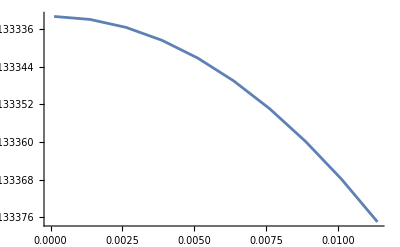

```mathematica
vintra=3;vinter=vintra/2;
dat1=Table[Quiet[sig[B,vintra,vinter]],{B,0.1,10,1}]
list=dat1;
len=Length[list];
scale=1(*list[[1,2]]*);
list=dat1;
len=Length[list];
scale=1(*list[[1,2]]*);
rathalf=Table[{list[[i,2]],list[[i,3]] scale},{i,1,len}];
ListLinePlot[{rathalf}]
```

{{7,0.000125,-8.33333×10^-6},{7,0.001375,-8.33334×10^-6},{7,0.002625,-8.33334×10^-6},{7,0.003875,-8.33335×10^-6},{7,0.005125,-8.33337×10^-6},{7,0.006375,-8.33339×10^-6},{7,0.007625,-8.33342×10^-6},{7,0.008875,-8.33345×10^-6},{7,0.010125,-8.33348×10^-6},{7,0.011375,-8.33352×10^-6}}

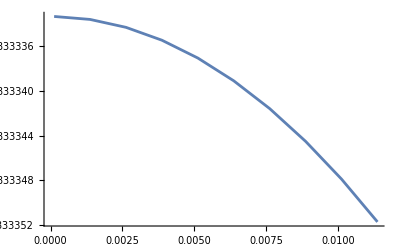

```mathematica
vintra=3;vinter=vintra;
dat1=Table[Quiet[sig[B,vintra,vinter]],{B,0.1,10,1}]
list=dat1;
len=Length[list];
scale=1(*list[[1,2]]*);
list=dat1;
len=Length[list];
scale=1(*list[[1,2]]*);
rat1=Table[{list[[i,2]],list[[i,3]] scale},{i,1,len}];
ListLinePlot[{rat1}]
```

{{7,0.000125,-4.7619×10^-6},{7,0.001375,-4.7619×10^-6},{7,0.002625,-4.76188×10^-6},{7,0.003875,-4.76184×10^-6},{7,0.005125,-4.7618×10^-6},{7,0.006375,-4.76174×10^-6},{7,0.007625,-4.76166×10^-6},{7,0.008875,-4.76158×10^-6},{7,0.010125,-4.76148×10^-6},{7,0.011375,-4.76137×10^-6}}

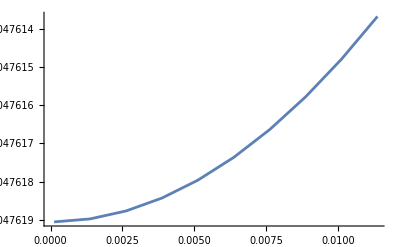

```mathematica
vintra=3;vinter=2vintra;
dat1=Table[Quiet[sig[B,vintra,vinter]],{B,0.1,10,1}]
list=dat1;
len=Length[list];
scale=1(*list[[1,2]]*);
list=dat1;
len=Length[list];
scale=1(*list[[1,2]]*);
rat2=Table[{list[[i,2]],list[[i,3]] scale},{i,1,len}];
ListLinePlot[{rat2}]
```

### final calcu with finite energy offset

```mathematica
Clear[sigd,B,βintra,βinter,γ,vomm1,vomm2,vdotk1,vdotk2,vvec,kf1,mvec1];

sigd[B_,βintra_,βinter_]:=Block[{e=1,μ=0.1,Δ=0.01,vf=0.005,vvec,Ωvec1,mvec1,Ωvec2,mvec2,θ,ϕ,kf1,kf2,θp,chi,Dphase1,Dphase2,vomm1,vomm2,vdotk1,vdotk2,f1,f2,τ1,τ2,h1,h2,zero1,zero2,ct41,ct42,st41,st42,ct4ct41,ct4ct42,st4st41,st4st42,ct4st41,ct4st42,st21,st22,st4st21,st4st22,ct4st21,ct4st22,st2st21,st2st22,hzero1,hzero2,hct41,hct42,hst41,hst42,hst21,hst22,colvec,mat,sol,Λ1,Λ2,s1,s2,λ1,a1,b1,c1,λ2,a2,b2,c2,int1,int2,conteq,matr,totmat},

chi=1;
kf1[θ_]=(μ+√(μ^2-2 B chi e vf^2 Cos[θ]))/(2 vf);
vvec[θ_]={ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}vf;
vomm1[θ_]=(-B chi e vf)/kf1[θ]^2{ Cos[ϕ] Sin[θ]Cos[θ],Sin[θ]Cos[θ] Sin[ϕ],-B chi e vf Cos[2 θ]};

Dphase1[θ_]=1-(B chi e Cos[θ])/kf1[θ]^2;
vdotk1[θ_]=vf kf1[θ] -(B e vf chi Cos[θ])/(2 kf1[θ]);
h1[θ_]=1/Dphase1[θ](vf Cos[θ]-(B chi e vf Cos[2 θ])/(2 kf1[θ]^2)+(B chi e vf (B chi e Cos[θ]-2 kf1[θ]^2))/(2 kf1[θ]^4));

(******** second node ***************)
chi=-1;
kf2[θ_]=(μ+Δ+√((μ+Δ)^2-2 B chi e vf^2 Cos[θ]))/(2 vf);
vomm2[θ_]={-(B chi e vf Cos[θ] Cos[ϕ] Sin[θ])/kf2[θ]^2,-(B chi e vf Cos[θ] Sin[θ] Sin[ϕ])/kf2[θ]^2,-(B chi e vf Cos[2 θ])/(2 kf2[θ]^2)};

Dphase2[θ_]=1-(B chi e Cos[θ])/kf2[θ]^2;
vdotk2[θ_]=vf kf2[θ]-(B e vf chi Cos[θ])/(2 kf2[θ]);
h2[θ_]=1/Dphase2[θ](vf Cos[θ]-(B chi e vf Cos[2 θ])/(2 kf2[θ]^2)+(B chi e vf (B chi e Cos[θ]-2 kf2[θ]^2))/(2 kf2[θ]^4));
(**********************************************************************************************************************************************)
(* -Graphics- ; -Graphics-*)
τ1[θ_]=(βintra Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp] Cos[θp/2]^4,{θp,0,π}]+
βintra Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp] Sin[θp/2]^4,{θp,0,π}]+(βintra Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}]+
(***** conjugate node  *****)
βinter Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp] Cos[θp/2]^4,{θp,0,π}]+βinter Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp] Sin[θp/2]^4,{θp,0,π}]+(βinter Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}])^-1;

τ2[θ_]=(βintra Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp] Cos[θp/2]^4,{θp,0,π}]+
βintra Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp] Sin[θp/2]^4,{θp,0,π}]+(βintra Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}]+
(***** conjugate node  *****)
βinter Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp] Cos[θp/2]^4,{θp,0,π}]+βinter Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp] Sin[θp/2]^4,{θp,0,π}]+(βinter Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}])^-1;
(*-Graphics-*)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];

f2[θ_]=(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]] Dphase2[θ] τ2[θ];
(* Ref. PRB 103,115146 (2021) *)
zero1=Quiet[NIntegrate [f1[θ],{θ,0,π}]];
zero2=Quiet[NIntegrate [f2[θ],{θ,0,π}]];
ct41=Quiet[NIntegrate [f1[θ] Cos[θ/2]^4,{θ,0,π}]];
ct42=Quiet[NIntegrate [f2[θ] Cos[θ/2]^4,{θ,0,π}]];
st41=Quiet[NIntegrate [f1[θ] Sin[θ/2]^4,{θ,0,π}]];
st42=Quiet[NIntegrate [f2[θ] Sin[θ/2]^4,{θ,0,π}]];
st21=Quiet[NIntegrate [f1[θ] Sin[θ]^2,{θ,0,π}]];
st22=Quiet[NIntegrate [f2[θ] Sin[θ]^2,{θ,0,π}]];
st2st21=Quiet[NIntegrate [f1[θ] Sin[θ]^4,{θ,0,π}]];
st2st22=Quiet[NIntegrate [f2[θ] Sin[θ]^4,{θ,0,π}]];
ct4ct41=Quiet[NIntegrate [f1[θ] Cos[θ/2]^8,{θ,0,π}]];
ct4ct42=Quiet[NIntegrate [f2[θ] Cos[θ/2]^8,{θ,0,π}]];
ct4st21=Quiet[NIntegrate [f1[θ] Cos[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
ct4st22=Quiet[NIntegrate [f2[θ] Cos[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st4st41=Quiet[NIntegrate [f1[θ] Sin[θ/2]^8,{θ,0,π}]];
st4st42=Quiet[NIntegrate [f2[θ] Sin[θ/2]^8,{θ,0,π}]];
ct4st41=Quiet[NIntegrate [f1[θ] Cos[θ/2]^4 Sin[θ/2]^4,{θ,0,π}]];
ct4st42=Quiet[NIntegrate [f2[θ] Cos[θ/2]^4 Sin[θ/2]^4,{θ,0,π}]];
st4st21=Quiet[NIntegrate [f1[θ] Sin[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st4st22=Quiet[NIntegrate [f2[θ] Sin[θ/2]^4 Sin[θ]^2,{θ,0,π}]];

hzero1=Quiet[NIntegrate [f1[θ]h1[θ],{θ,0,π}]];
hzero2=Quiet[NIntegrate [f2[θ]h2[θ],{θ,0,π}]];
hct41=Quiet[NIntegrate [f1[θ] h1[θ] Cos[θ/2]^4,{θ,0,π}]];
hct42=Quiet[NIntegrate [f2[θ] h2[θ] Cos[θ/2]^4,{θ,0,π}]];
hst41=Quiet[NIntegrate [f1[θ] h1[θ] Sin[θ/2]^4,{θ,0,π}]];
hst42=Quiet[NIntegrate [f2[θ] h2[θ] Sin[θ/2]^4,{θ,0,π}]];
hst21=Quiet[NIntegrate [f1[θ] h1[θ] Sin[θ]^2,{θ,0,π}]];
hst22=Quiet[NIntegrate [f2[θ] h2[θ] Sin[θ]^2,{θ,0,π}]];

colvec=({{0}, {hst42 βinter+hct41 βintra}, {hct42 βinter+hst41 βintra}, {1/4(hst22 βinter+hst21 βintra)}, {0}, {hst41 βinter+hct42 βintra}, {hct41 βinter+hst42 βintra}, {1/4 (hst21 βinter+hst22 βintra)}});
matr=({{1, 0, 0, 0, 0, 0, 0, 0}, {-ct41 βintra, 1-ct4ct41 βintra, -ct4st41 βintra, -ct4st21 βintra, -st42 βinter, -ct4st42 βinter, - st4st42 βinter, -st4st22 βinter}, {-st41 βintra, -ct4st41 βintra, 1-st4st41 βintra, -st4st21 βintra, -ct42 βinter, -ct4ct42 βinter, -ct4st42 βinter, -ct4st22 βinter}, {-1/4 st21 βintra, -1/4 ct4st21 βintra, -1/4 st4st21 βintra, 1-1/4 st2st21 βintra, -1/4 st22 βinter, -1/4 ct4st22 βinter, -1/4  st4st22 βinter, -1/4 st2st22 βinter}, {0, 0, 0, 0, 1, 0, 0, 0}, {-st41 βinter, -ct4st41 βinter, -st4st41 βinter, -st4st21 βinter, -ct42 βintra, 1-ct4ct42 βintra, -ct4st42 βintra, -ct4st22 βintra}, {-ct41 βinter, -ct4ct41 βinter, -ct4st41 βinter, -ct4st21 βinter, -st42 βintra, -ct4st42 βintra, 1-st4st42 βintra, -st4st22 βintra}, {-1/4 st21 βinter, -1/4 ct4st21 βinter, -1/4 st4st21 βinter, -1/4 st2st21 βinter, -1/4 st22 βintra, -1/4 ct4st22 βintra, -1/4 st4st22 βintra, 1-1/4 st2st22 βintra}}) ;
mat=matr.({{λ1}, {a1}, {b1}, {c1}, {λ2}, {a2}, {b2}, {c2}});  conteq=(a1 ct41-hzero1+c1 st21+b1 st41+λ1 zero1) +(a2 ct42-hzero2+c2 st22+b2 st42+λ2 zero2)  ;
totmat=mat+colvec;
sol=Flatten[Solve[{totmat[[1]]==0,totmat[[2]]==0,totmat[[3]]==0,totmat[[4]]==0,totmat[[5]]==0,totmat[[6]]==0,totmat[[7]]==0,totmat[[8]]==0,conteq==0},{λ1,a1,b1,c1,λ2,a2,b2,c2}],1]//Chop;

Λ1[θ_]=τ1[θ](a1 Cos[θ/2]^4-h1[θ]+c1 Sin[θ]^2+b1 Sin[θ/2]^4+λ1)/.sol;    
Λ2[θ_]=τ2[θ](a2 Cos[θ/2]^4-h2[θ]+c2 Sin[θ]^2+b2 Sin[θ/2]^4+λ2)/.sol;
int1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]](vf Cos[θ]-(B e vf Cos[2 θ])/(2 kf1[θ]^2)+(B e vf (B e Cos[θ]-2 kf1[θ]^2))/(2 kf1[θ]^4))Λ1[θ];
int2[θ_]=(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]](vf Cos[θ]+(B e vf Cos[2 θ])/(2 kf2[θ]^2)+(B e vf (B e Cos[θ]+2 kf2[θ]^2))/(2 kf2[θ]^4) )Λ2[θ];
s1=NIntegrate[int1[θ],{θ,0,π}];
s2=NIntegrate[int2[θ],{θ,0,π}];
{MatrixRank[matr],(e B vf^2)/(2 μ^2),s1+s2,MatrixForm[{λ1,a1,b1,c1,λ2,a2,b2,c2}/.sol]}
];
sigd[10,1,0.5]
```

{7,0.0125,-0.0000401095,(0
-0.00057452
0.000670095
0.0000200516
0
-0.00142948
0.00133479
-0.0000204964)}

```mathematica
{7,0.012499999999999997,-0.00004001581329457507}
```

## Results

```mathematica
vintra=3;vinter=vintra/2;
dat1=Table[Quiet[sigd[B,vintra,vinter]],{B,0.1,10,1}];
```

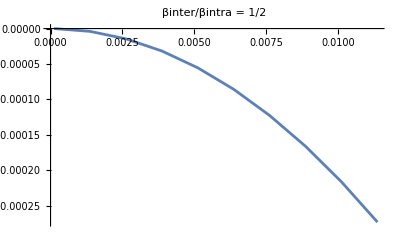

```mathematica
list={{7,0.00012499999999999998,-0.00001336541863529968},{7,0.001375,-0.000013365471529479533},{7,0.0026249999999999997,-0.000013365612583362598},{7,0.0038749999999999995,-0.000013365841804413497},{7,0.0051249999999999985,-0.000013366159204764356},{7,0.006374999999999999,-0.000013366564801217799},{7,0.007624999999999998,-0.000013367058615251134},{7,0.008874999999999997,-0.00001336764067302169},{7,0.010124999999999999,-0.000013368311005373293},{7,0.011374999999999998,-0.000013369069647843957}};
len=Length[list];
scale=1/Abs[list[[1,3]]];sh=-1;
rathalf=Table[{list[[i,2]],list[[i,3]] scale-sh},{i,1,len}];
p1=ListLinePlot[{rathalf},PlotLabel->"βinter/βintra = 1/2"]
```

```mathematica
vintra=3;vinter=vintra;
dat1=Table[Quiet[sigd[B,vintra,vinter]],{B,0.1,10,1}]
```

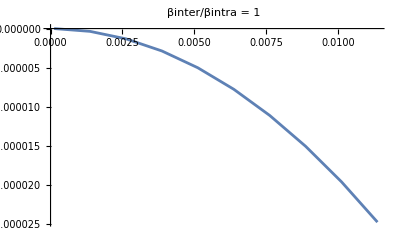

```mathematica
list={{7,0.00012499999999999998,-8.40857751809503*^-6},{7,0.001375,-8.408580535196183*^-6},{7,0.0026249999999999997,-8.408588581733788*^-6},{7,0.0038749999999999995,-8.408601660256884*^-6},{7,0.0051249999999999985,-8.408619774908639*^-6},{7,0.006374999999999999,-8.408642931427791*^-6},{7,0.007624999999999998,-8.4086711371506*^-6},{7,0.008874999999999997,-8.408704401013374*^-6},{7,0.010124999999999999,-8.408742733555524*^-6},{7,0.011374999999999998,-8.408786146923198*^-6}};
len=Length[list];
scale=1/Abs[list[[1,3]]];sh=-1;
rathalf=Table[{list[[i,2]],list[[i,3]] scale-sh},{i,1,len}];
p2=ListLinePlot[{rathalf},PlotLabel->"βinter/βintra = 1"]
```

```mathematica
vintra=3;vinter=2vintra;
dat1=Table[Quiet[sigd[B,vintra,vinter]],{B,0.1,10,1}]
```

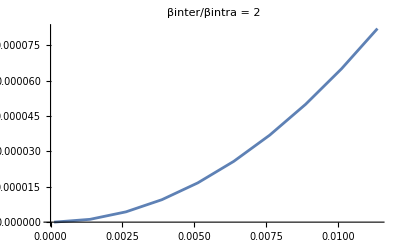

```mathematica
list={{7,0.00012499999999999998,-4.843979566151475*^-6},{7,0.001375,-4.8439738039528135*^-6},{7,0.0026249999999999997,-4.843958438355781*^-6},{7,0.0038749999999999995,-4.843933470086179*^-6},{7,0.0051249999999999985,-4.843898900323884*^-6},{7,0.006374999999999999,-4.843854730703521*^-6},{7,0.007624999999999998,-4.8438009633153625*^-6},{7,0.008874999999999997,-4.843737600706505*^-6},{7,0.010124999999999999,-4.843664645882289*^-6},{7,0.011374999999999998,-4.843582102307981*^-6}};
len=Length[list];
scale=1/Abs[list[[1,3]]];sh=-1;
rat2=Table[{list[[i,2]],list[[i,3]] scale-sh},{i,1,len}];
p3=ListLinePlot[{rat2}, PlotLabel->"βinter/βintra = 2"]
```

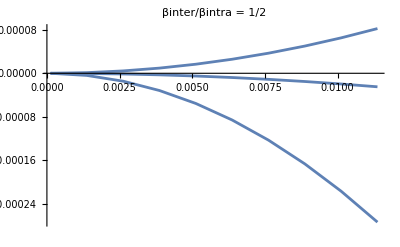

```mathematica
Show[{p1,p2,p3},PlotRange->All]
```